### Load Trajectory3D package

Package available at Github, download and use path name.

```mathematica
$UserBaseDirectory
```

/Users/dinesh/Library/Wolfram

```mathematica
Get["/Users/dinesh/Dropbox/MyPackages/Trajectory3D.wl"]
Names["Trajectory3D`*"]
```

{AngleofFlight,CollettPlot3D,DistanceProfile3D,GetData3D,InputUserValues3D,OrthogonalComponentsVelocity3D,ProximityCut3D,SpeedCollettPlot3D,SpeedProfile3D,TwinCollettPlot3D}

### Import Data

project specific constants and other variables

```mathematica
fps = 1/500;(*frame rate*)
a = FileNames[All,"/Users/dinesh/Dropbox/projects/lynx/lynx prey response/Data/data_posed3D/control"];
b=FileBaseName[#]&/@a;
c=Select[a,StringContainsQ[#,"white"]&];
d = Select[a,StringContainsQ[#,"yellow"]&];
whitecontrol=Import[#,"Data", HeaderLines->1]&/@c;
yellowcontrol = Import[#,"Data", HeaderLines->1]&/@d;
```

```mathematica
whitecontrol//Dimensions
```

{5}

```mathematica
yellowcontrol//Dimensions
```

{3}

### Speed

```mathematica
yellowcontrolspeeds={DistanceProfile3D[yellowcontrol[[#]]],SpeedProfile3D[yellowcontrol[[#]]]}ᵀ&/@{1,2,3};
```

```mathematica
SmoothDensityHistogram[Flatten[yellowcontrolspeeds,1],PlotRange->{{0,30},{0,200}},FrameLabel->{{HoldForm["Speed (cm/s)"],None},{HoldForm["Distance from flower (cm)"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

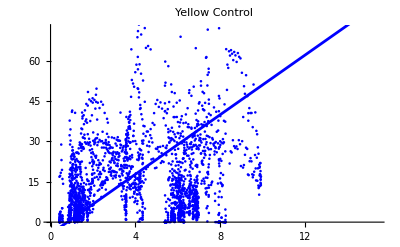

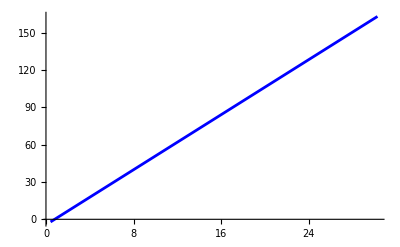

| Estimate | Standard Error | t-Statistic | P-Value
1 | -4.39414 | 0.799294 | -5.49752 | 4.23823×10^-8
x | 5.52751 | 0.137643 | 40.1583 | 4.22892×10^-273

```mathematica
yc=Flatten[yellowcontrolspeeds,1];
ycmodel=LinearModelFit[yc,x,x];
Show[
  ListPlot[yc,PlotStyle->Blue,PlotLabel->"Yellow Control"],
  Plot[ycmodel[x],{x,Min[yc[[All,1]]],Max[yc[[All,1]]]},PlotStyle->Blue]
]
Plot[ycmodel[x],{x,Min[yc[[All,1]]],Max[yc[[All,1]]]},PlotStyle->Blue]
ycmodel["ParameterTable"]
```

```mathematica
whitecontrolspeeds={DistanceProfile3D[whitecontrol[[#]]],SpeedProfile3D[whitecontrol[[#]]]}ᵀ&/@{1,2,3,4,5};
```

```mathematica
SmoothDensityHistogram[Flatten[whitecontrolspeeds,1],PlotRange->{{0,30},{0,200}},FrameLabel->{{HoldForm["Speed (cm/s)"],None},{HoldForm["Distance from flower (cm)"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

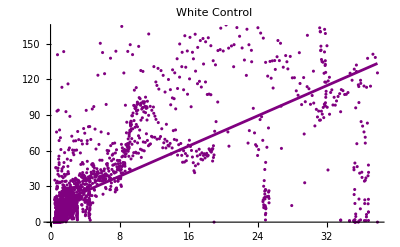

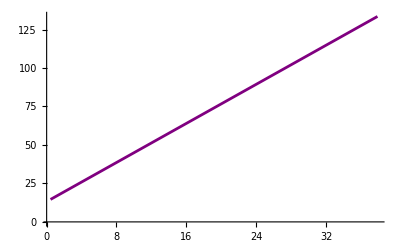

| Estimate | Standard Error | t-Statistic | P-Value
1 | 13.1878 | 0.917599 | 14.3721 | 7.74664×10^-45
x | 3.17565 | 0.0777156 | 40.8625 | 3.7091×10^-272

```mathematica
wc=Flatten[whitecontrolspeeds,1];
wcmodel=LinearModelFit[wc,x,x];
Show[
  ListPlot[wc,PlotStyle->Purple,PlotLabel->"White Control"],
  Plot[wcmodel[x],{x,Min[wc[[All,1]]],Max[wc[[All,1]]]},PlotStyle->Purple]
]
Plot[wcmodel[x],{x,Min[wc[[All,1]]],Max[wc[[All,1]]]},PlotStyle->Purple]
wcmodel["ParameterTable"]
```

#### Compare speed/distance slopes (spider vs control)

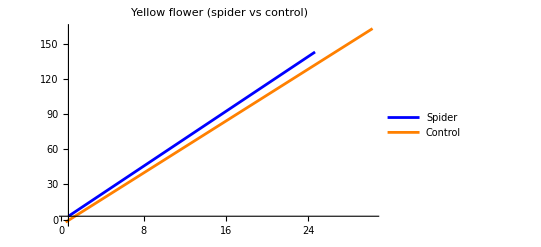

```mathematica
Show[
  Plot[ymodel[x],{x,Min[ydata[[All,1]]],Max[ydata[[All,1]]]},
    PlotStyle->Blue,PlotLegends->LineLegend[{"Spider"},LegendMarkerSize->Medium], PlotRange->All],
  Plot[ycmodel[x],{x,Min[yc[[All,1]]],Max[yc[[All,1]]]},
    PlotStyle->Orange,PlotLegends->LineLegend[{"Control"},LegendMarkerSize->Medium]],
  PlotLabel->"Yellow flower (spider vs control)"
]
```

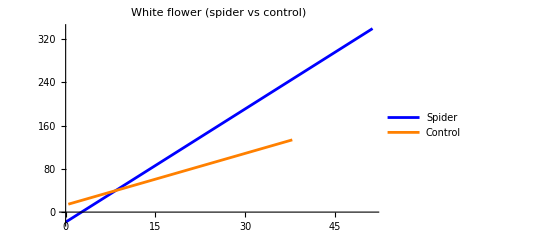

```mathematica
Show[
  Plot[wmodel[x],{x,Min[wdata[[All,1]]],Max[wdata[[All,1]]]},
    PlotStyle->Blue,PlotLegends->LineLegend[{"Spider"},LegendMarkerSize->Medium],PlotRange->All],
  Plot[wcmodel[x],{x,Min[wc[[All,1]]],Max[wc[[All,1]]]},
    PlotStyle->Orange,PlotLegends->LineLegend[{"Control"},LegendMarkerSize->Medium]],
  PlotLabel->"White flower (spider vs control)"
]
```

#### Test for differences in slope

yellow

```mathematica
model1 =ymodel;
model2 =ycmodel;

(* Extract parameter information including slopes *)
(* Get the slope coefficients and their standard errors *)
slope1 = model1["BestFitParameters"][[2]];
slope2 = model2["BestFitParameters"][[2]];
stderr1 = model1["ParameterErrors"][[2]];
stderr2 = model2["ParameterErrors"][[2]];

(* Calculate the difference between slopes *)
slopeDiff = slope1 - slope2;

(* Calculate standard error of the difference *)
seDiff = Sqrt[stderr1^2 + stderr2^2];

(* Calculate t-statistic *)
tStat = slopeDiff/seDiff;

(* Extract degrees of freedom from ANOVA tables correctly *)
anovaTable1 = model1["ANOVATable"];
anovaTable2 = model2["ANOVATable"];

(* Find the Error row in each ANOVA table *)
df1 = Cases[anovaTable1, {"Error", df_, ___} :> df, Infinity][[1]];
df2 = Cases[anovaTable2, {"Error", df_, ___} :> df, Infinity][[1]];


(* Use the pooled degrees of freedom *)
df = df1 + df2;

(* Calculate p-value (two-tailed test) *)
pValue = 2 * (1 - CDF[StudentTDistribution[df], Abs[tStat]]);

(* Print results *)
Print["Slope 1: ", slope1, " ± ", stderr1];
Print["Slope 2: ", slope2, " ± ", stderr2];
Print["Difference: ", slopeDiff, " ± ", seDiff];
Print["t-statistic: ", tStat];
Print["Degrees of freedom: ", df];
Print["p-value: ", pValue];
Print["Significant difference at α=0.05: ", pValue < 0.05]
```

Slope 1: 5.83697 ± 0.147782

Slope 2: 5.52751 ± 0.137643

Difference: 0.309457 ± 0.201954

t-statistic: 1.53232

Degrees of freedom: 4961

p-value: 0.125508

Significant difference at α=0.05: False

white

```mathematica
model1 =wmodel;
model2 =wcmodel;

(* Extract parameter information including slopes *)
(* Get the slope coefficients and their standard errors *)
slope1 = model1["BestFitParameters"][[2]];
slope2 = model2["BestFitParameters"][[2]];
stderr1 = model1["ParameterErrors"][[2]];
stderr2 = model2["ParameterErrors"][[2]];

(* Calculate the difference between slopes *)
slopeDiff = slope1 - slope2;

(* Calculate standard error of the difference *)
seDiff = Sqrt[stderr1^2 + stderr2^2];

(* Calculate t-statistic *)
tStat = slopeDiff/seDiff;

(* Extract degrees of freedom from ANOVA tables correctly *)
anovaTable1 = model1["ANOVATable"];
anovaTable2 = model2["ANOVATable"];

(* Find the Error row in each ANOVA table *)
df1 = Cases[anovaTable1, {"Error", df_, ___} :> df, Infinity][[1]];
df2 = Cases[anovaTable2, {"Error", df_, ___} :> df, Infinity][[1]];


(* Use the pooled degrees of freedom *)
df = df1 + df2;

(* Calculate p-value (two-tailed test) *)
pValue = 2 * (1 - CDF[StudentTDistribution[df], Abs[tStat]]);

(* Print results *)
Print["Slope 1: ", slope1, " ± ", stderr1];
Print["Slope 2: ", slope2, " ± ", stderr2];
Print["Difference: ", slopeDiff, " ± ", seDiff];
Print["t-statistic: ", tStat];
Print["Degrees of freedom: ", df];
Print["p-value: ", pValue];
Print["Significant difference at α=0.05: ", pValue < 0.05]
```

General::munfl: Exp[-1064.36] is too small to represent as a normalized machine number; precision may be lost.

Slope 1: 6.97139 ± 0.123872

Slope 2: 3.17565 ± 0.0777156

Difference: 3.79574 ± 0.146232

t-statistic: 25.9569

Degrees of freedom: 5012

p-value: 0.

Significant difference at α=0.05: True

### Persistence velocity

```mathematica
pvyc = OrthogonalComponentsVelocity3D[yellowcontrol[[#]]][[1]]&/@{1,2,3}
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{6.11652,-183.046,-20.9697,174.587,-190.984,112.47,-130.586,181.829,-14.2045,-5.90666,114.373,-153.342,226.689,-162.069,66.3873,47.1165,-79.7481,190.838,-119.158,120.073,-276.896,58.9484,-172.079,3.07292,-67.2279,196.055,-1.14302,-144.801,8.67035,95.4582,-110.691,-41.0905,35.9792,94.5146,-40.9458,125.718,-49.5399,0.,-6.97785,15.2231,-48.1832,-23.1105,45.5081,-104.267,4.56312,101.84,-19.1119,-343.166,27.1639,-24.1542,-32.786,-3.68384,-9.76235,2.86985,-140.479,50.0036,-51.3427,41.6335,-26.3656,1.15346,-285.277,46.2983,-13.81,12.6151,-47.7224,7.92817,2.60207,43.6923,-15.4904,-6.83745,-59.0946,1.88208,-23.0733,25.1176,-12.737,-58.9238,52.7687,2.9475,-83.0376,-22.7917,-29.2169,18.7182,16.4824,37.9656,-60.6987,-3.05669,-37.4864,6.63557,15.3183,-29.2239,-34.5318,19.5386,-13.8926,2.13349,6.75744,-6.2473×10^-17,-0.293089,1.47991,33.8264,-37.0589,-7.09503,20.8964,18.6084,-27.3889,6.02244,-2.88538,17.0071,-22.2561,15.335,12.9373,15.4809,-20.9999,5.92866,-83.6983,19.8946,-0.276546,56.4071,12.1775,-8.95214,-65.0322,47.19,-15.3881,30.7891,41.9135,-19.7513,2.4259,15.1614,-0.64511,2.16869,-18.547,25.6928,-32.6152,-20.6389,-0.826663,32.44,-20.5336,-2.77307,24.0308,-11.411,35.3616,-46.4568,30.6448,60.8748,-6.03741,29.9827,-34.8282,-33.1381,132.586,-27.0385,26.0971,-56.0894,-54.0701,-16.1974,10.3184,-9.57001,28.0293,184.349,-1.79314,11.1823,-14.472,-2.70209,1.26275,-0.810654,0.598139,0.485009,1707.55,-1.77735×10^-15,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,178.902,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-271.916,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.0699788,-23.2444,79.8323,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,5.62098,-2.92952×10^-14,0.,-119.959,-0.821745,51.6155,119.586,0.525176,-118.703,103.858,66.0836,135.685,-16.261,-9.3449,0.,-0.0911031,-2.38494,0.009523,-12.3911,413.809,0.,0.0766245,-0.927685,-25.0806,0.,-57.8052,748.995,0.,31.4575,-94.7929,6.34119,72.6823,-83.3743,0.,65.712,0.19109,-2.43635,-76.1043,0.,-11.6593,203.035,-12.4985,61.2935,54.4543,-8.61347,-70.1368,79.0386,-5.29681,-6.59278,12.6184,-8.92925,6.48931×10^-16,-18.7285,0.,-9.01319,147.526,3.81474,9.69594,-0.475402,0.172166,-1.00678,-6.9247,8.15999,6.5123,-306.865,-1.55025,0.320558,2.82118,1.07889,-77.5131,0.,-8.64126,182.952,0.,5.9118,-31.5665,-16.3955,0.,-1.17905,1.82873,0.43037,-35.703,0.66383,0.995287,-0.438495,0.568366,-0.303978,-1.05754,-30.8955,253.58,-7.63796,-0.376772,1.85826,-1.77399,1.95589,-0.29215,0.351898,0.13346,0.140435,-0.25671,2.12052,1.06919,-0.663883,-4.38857,7.02696,-6.14184,-1.5452×10^-16,0.,-0.190317,-0.679282,146.15,0.811648,-22.104,6.2259,-2.26761,0.446985,-0.96748,0.489992,-2.33581,0.775252,-0.697728,0.564178,-0.392514,-24.98,50.7942,-11.4599,-50.3847,23.5582,46.61,-10.4728,7.46388,0.,36.7019,-35.7173,-1.73079,-1.84937,-69.1473,9.23201,41.679,20.5997,4.20815,4.21215,31.1006,-10.7269,-7.94585,-7.85795,18.6224,21.8501,-20.3443,14.7617,-8.82844,-12.6006,-5.36464,55.6175,-14.9975,-1.45422,43.4438,12.4513,-5.58267,-18.7582,Indeterminate,Indeterminate,0.242153,Indeterminate,Indeterminate,Indeterminate,2.42302,-14.6401,19.0425,0.,23.8537,-20.6128,2.76007,-5.19106,0.,50.2414,-1.55008,-24.6752,13.8355,-15.4122,-8.75076,-3.94943,-46.581,22.9627,-12.6637,4.31122,-46.9259,48.4603,58.536,0.,0.,0.,-84.3244,-35.0747,-37.0329,95.7648,-37.8127,-28.6128,27.221,-68.3457,29.9052,-27.2865,30.8507,-6.05195,14.0094,78.7635,14.4904,-8.43617,-35.6265,2.48319,6.37594,11.533,13.8703,39.3238,-111.477,104.135,-130.682,112.669,0.,-30.73,25.4489,9.79203,-151.735,67.5399,69.9168,-54.64,-22.1391,47.4001,19.6774,-78.5701,-43.9743,-53.7058,187.804,0.,206.241,-247.96,-215.961,-1.26829,63.883,140.906,-49.8618,-25.503,8.15503,104.29,-90.1273,183.661,-163.846,27.347,3.15653,-75.2768,0.,34.3254,-11.4964,-37.4494,134.254,Indeterminate,Indeterminate,76.1646,8.84275×10^-15,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,22.7128,301.245,-11.2643,62.3151,-16.3183,-35.2916,64.1939,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,-9.73733×10^-17,389.97,14.4897,Indeterminate,Indeterminate,Indeterminate,241.137,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,17.2082,-61.4981,22.51,7.6149,49.6309,-44.0731,59.5878,-65.6862,185.642,-20.9262,-59.5158,-55.839,96.0097,-18.594,27.1559,-2.63431,62.7833,-142.278,-5.0941,-62.9484,128.108,-14.5168,-74.6953,-45.5097,48.8635,-17.771,24.392,-152.62,0.,-20.2356,-89.6062,72.6852,-22.0487,35.2743,0.,102.451,-64.005,10.6807,-8.48265,-9.38603,-8.3305,39.9185,15.788,-61.5653,39.331,-27.7918,-1.95871,0.,-3.76267,-2.28123,0.191782,3.80589,-9.63559,-11.1142,4.79306,-11.6151,1.24135,0.705476,-4.8889,8.52932,1.75137,-3.56996,-9.23852,-5.88914,23.5594,-7.05343,24.5537,-7.42017,4.89181,0.315098,17.4835,-11.3272,47.702,12.8639,-14.5089,33.2041,-12.8655,16.2643,41.8308,-2.5585,-33.1145,-9.12458,4.02647,17.3462,59.7504,-4.25693,-70.5328,36.4355,42.4911,14.535,-60.6796,-6.25105,-1.0086,18.11,40.3981,-20.4352,-3.96809,-15.7587,43.8314,-4.74615,38.3363,0.,17.0651,20.1572,1.36452,-6.89315,-2.18864,8.63351,-4.05025,-1.6085,10.5046,-5.1305,2.24765,6.44343,-1.3048,1.7882,13.6738,2.66293,-15.3682,-27.7026,17.2665,-31.5962,33.731,-54.8163,44.0031,31.7436,-96.08,-12.5203,0.380845,0.850313,-1.11182,0.,3.34766,7.00487,26.507,-21.1453,10.2814,-16.2951,19.7315,7.5188,21.9424,-62.8425,31.6817,15.0025,-21.4031,-2.50638,14.1437,-2.74516,-11.1634,9.14897,-18.4125,13.111,-2.46392,6.00002,-10.1255,14.1966,-23.2633,-24.3819,32.1474,-31.6332,47.6097,-22.2143,-60.3248,1.202,-1.50171,9.78492,14.8635,-53.6572,0.,-5.07558,-11.2323,19.9447,0.,19.8628,-51.876,-4.26397,0.,-69.343,-3.73207,50.6135,0.,4.72205,17.3884,-28.8259,73.542,-35.4551,1.58511,0.242333,2.52267,-53.691,13.8904,0.,-6.58262,-0.676,35.9562,-55.5567,-4.74001,23.5261,-13.6711,13.227,-187.119,2.26694,2.33825×10^-17,Indeterminate,Indeterminate,Indeterminate,252.768,Indeterminate,Indeterminate,-1.49439,37.3729,-15.8518,1.1587,-104.564,-0.088361,-11.4454,2.81523,0.75349,3.98007,116.507,0.,58.8754,-43.6525,0.,-1.75495×10^-15,2.12246,1.73804,51.5435,-69.2852,4.18378,-2.88918,22.7316,3.54711,-68.6566,44.6405,-0.623027,-50.7687,15.0135,-2.13798,10.6164,-4.68935,14.7465,-18.3222,27.783,2.79716,35.0684,-22.2026,-11.2157,-48.9926,-9.52737,15.0343,1.61715,-1.76515,6.30327,16.5195,-40.3439,6.48472,-4.31808×10^-16,7.33314,0.,-7.57788,5.18568,-7.70057,7.67301,-5.18596,-1.4728,-5.25834,22.1089,-1.83661,17.7582,-3.34022,-12.9504,8.47685,25.0488,22.164,-4.61048,-17.134,-44.4928,41.7202,-25.2308,8.18746,24.8186,-14.7324,6.13684,45.7935,0.,14.7607,-20.7374,0.,-26.2393,36.1403,14.3465,-273.511,3.14101,69.656,36.8671,30.9259,-29.8968,8.12859,0.,-4.91921,-33.4337,77.8413,-238.8,83.5889,-277.071,8.60299,30.3516,-180.804,70.334,9.09393,-307.578,161.636,-387.26,52.8065,-215.526,66.2777,66.7622,-130.806,10.6461,-108.795,175.024,-58.3537,109.35,-377.675,0.,-180.641,398.973,0.655555,27.903,292.48,-155.723,37.6169,137.975,-251.924,0.,-57.6842,46.2776,-28.268,-8.35966,41.5514,91.9961,-115.392,19.284,0.,0.,0.,87.2117,-98.5463,-40.8606,33.2244,92.2339,-131.291,-12.7151,-5.23285,53.6138,-91.8593,9.48007,46.5899,-12.7476,125.746,-123.38,-22.7149,-13.4281,-3.56101,81.7165,-8.98838,59.1674,-43.1624,-17.9171,49.8013,-56.3526,-31.5034,10.5147,-9.41534,-14.2096,0.,-43.4042,-10.627,18.5667,-74.811,73.072,-45.5756,14.3057,36.6159,-73.1922,107.011,0.,16.0174,-14.033,19.7818,-7.64378,4.84511,-17.6893,0.,-16.2451,-75.7544,22.1039,28.6974,-41.2498,10.0895,72.2751,0.,100.222,25.3494,38.0185,-52.1832,-36.0955,19.0231,-68.503,-13.2713,0.,0.,0.,145.161,-129.183,-17.4201,-18.1172,-3.73087,0.806708,9.58012,20.6771,-9.75586,-0.0179178,71.6302,-19.3417,-31.4348,25.8955,-24.922,6.61187,4.40341,-4.65969,7.15583,-0.232976,2.5333,-26.3739,23.3714,-10.1374,10.633,24.8318,-46.9006,5.04698,-1.0449,0.,0.621293,2.97583,2.87115,-30.9233,3.10304,18.1313,-14.2314,-18.1391,0.,5.87933,-10.1235,23.3087,-27.0158,15.0669,2.97902,19.1253,-44.7665,0.,-31.6325,8.18248,25.6395,-16.6827,-56.7466,20.7749,-13.5364,70.8523,-75.4992,57.9614,-11.7816,27.376,13.1378,0.,0.,0.,-13.5803,-8.41706,9.38106,6.95892,-48.2686,35.0456,-15.3487,296.666,0.,13.1682,-8.80538,17.379,-17.9125,10.794,-6.81351,4.88388,3.94971,-9.43669,7.13623,3.67438,-0.342225,-1.53823×10^-15,1.86211×10^-16,-2.85523,-7.67017,-2.31725,0.212726,-4.70755,3.47099×10^-16,-0.287006,-25.8377,-0.520607,-5.44357,17.2114,1.03373×10^-15,0.370104,-1.39124,5.64456,-40.52,14.4135,-1.02663,-2.1898,-2.32843,-8.76238,5.87846,-32.7448,-8.79551,-5.05269,0.,-10.2809,-25.0184,35.0038,0.,3.50287,9.15837,-21.0977,0.,6.70005,-0.536834,13.3409,5.94936,-12.0075,0.,-20.6853,15.1595,0.392145,0.0332594,17.7106,-4.83692,22.6491,5.0098,-1.6645,0.,1.09691,-0.695406,-0.402586,0.,-20.5983,-1.37631,49.9913,0.,2.07388,27.8453,-20.7653,-0.193865,2.51739,8.24079,4.70565,-9.93454,-10.0222,0.,7.57731,-14.7046,0.,7.77258,23.1218,-3.55038,-6.77023,6.46715,-37.8876,27.2832,-50.978,17.2323,-14.9137,4.41966,9.97466,-3.33389,-0.385076,5.30168,-7.63306,18.1419,-9.98942,-14.0727,2.76866,30.4324,0.,0.,29.9222,-13.5521,-0.804514,11.2792,42.3565,-3.35509,9.01381,12.1543,-15.0142,9.95692,-0.597742,-1.76515,4.91428,-6.43559,9.46392,-0.474719,21.1378,-7.75399,-1.63029,13.4212,-0.0992199,-5.83142,9.18225,-8.68995,Indeterminate,Indeterminate,5.18436,-4.72719,27.9469,-38.6587,0.3069,-8.12196,-10.9639,1.37922,-15.7219,1.65246,-0.0495128,0.689217,-1.87507,0.662958,0.593123,6.58238,-90.4958,16.0335,-96.859,0.,1.81389,17.368,0.,1.98354,2.2084,3.14789,4.09251,-4.05224,-5.47252,0.642442,-21.0193,13.7602,-10.3239,4.8445,3.73647,2.3013×10^-16,-3.19438,-39.8469,15.0681,14.1056,26.155,0.227327,-7.18158,-19.226,8.66466,1.46646,4.56447,4.39106,-4.56316,4.49237,-4.14131,4.41017,0.966378,-15.6086,-2.34669,5.14913,14.588,0.,14.6151,-13.1713,-2.15921,-1.52617,1.33888,0.118752,0.,2.70562,-5.58674,24.5295,-1.52365,-0.684516,2.35566,0.111222,-2.30908,-0.150815,-2.04551,3.79939,0.469121,2.48109,-1.7088,0.364444,-0.608099,0.723676,Indeterminate,Indeterminate,0.170123,-2.85201,Indeterminate,Indeterminate,-0.460045,6.86452,-8.93876,-2.16564,0.0591927,-0.321659,-1.60343,0.0112784,1.23369,-0.00746215,38.6401,9.81767,0.,38.4928,-86.6023,0.,-0.801906,-0.587338,0.0573807,0.320915,15.6585,-1.07386,7.40563,-12.2601,21.6524,-5.42008,-2.68275,-6.97388,-0.388302,-1.16929,2.58802,-6.7209,-11.8021,17.1918,0.,6.94607,0.465498,-5.1149,-1.30897,0.468307,-0.803871,-10.3166,0.,-1.90601,5.45047,0.,0.926009,-32.3815,2.57997,15.3167,-4.46195},{Indeterminate,42.684,124.081,-50.5535,49.1016,15.6059,-127.048,119.795,83.3276,-63.5105,16.5574,39.2147,-733.633,404.491,8.18462,-134.116,93.4057,-110.519,203.892,-102.131,-9.34082,146.835,-80.997,42.1019,-95.865,210.436,-187.546,-3.01779,-16.2196,103.527,-54.6439,85.4617,-119.64,93.3323,-91.2476,129.949,-12.728,54.0049,-133.327,87.5086,-60.9971,-158.853,76.1304,80.5942,-75.7764,897.428,-2105.62,273.675,-15.3785,-107.332,-51.1826,-16.3882,67.587,92.9759,31.7643,-34.4234,14.4455,-49.9895,59.4177,-25.288,1.41191,15.5728,49.5745,-85.606,16.5555,-40.1521,58.3081,34.1853,5.40303,6.53151,-92.7594,90.3985,-105.911,63.2807,-78.3214,64.9121,-120.841,609.505,-1360.68,39.4148,-15.4934,-56.4012,11.9187,26.3102,-61.5345,60.3349,-59.3721,41.4807,46.9238,-101.184,-55.4759,72.5498,-79.3047,74.734,9.79514,-10.4203,29.3066,75.4813,-14.9845,-14.1447,47.4372,23.3571,-123.021,-71.4567,102.319,50.7414,32.4405,43.3404,-54.189,-83.7181,0.,-105.428,-413.271,153.663,69.915,-18.8118,387.385,-258.087,-45.2105,-12.0201,-91.4319,-6.8363,-29.9949,0.,-46.5248,374.126,0.,7.47134,-90.4537,67.516,-77.0362,42.1832,-2.5784,4.50171,41.489,-60.6874,70.1835,47.2728,-2.29442,-104.768,0.870025,-0.90453,-0.736149,-60.7734,30.609,-10.2709,6.61325,-33.0373,34.5492,-69.6107,-80.3271,-50.1364,53.1323,19.7883,-2.52831,-7.66269,13.6028,0.,-80.1089,-18.8874,12.0503,-1.49608,196.085,0.,207.442,-221.842,0.,-39.2425,-105.493,18.121,14.2194,-70.8655,256.543,-111.919,87.2558,48.7104,452.786,-122.463,77.6818,0.,-10.949,10.3603,0.,30.8299,16.1432,35.2412,-56.1689,33.5246,-3.95454,59.4081,46.0775,52.4123,-6.47051,27.2334,-114.068,-57.0182,-21.8329,10.4998,-15.3065,11.7377,16.6243,10.2093,111.488,-2.82296,30.6835,52.6191,-153.672,-41.3003,-172.151,110.914,-2.85932,8.48341,-192.23,-17.8075,0.744966,-29.3586,74.17,78.7345,-21.6219,96.1878,-11.7923,60.1729,-45.2171,42.4687,-93.6967,-106.223,-56.9065,-53.9384,0.,-9.8755,-46.2082,-6.60659,101.775,0.,48.0745,-59.9621,12.403,-88.8895,-135.268,24.7323,-23.5515,3.18769,45.5547,112.362,-125.054,83.0733,-41.4242,157.205,-27.7352,-136.287,0.,-18.3201,88.6013,0.,122.011,31.2217,-261.498,0.,-2.91254,185.991,0.,143.326,-139.059,-50.539,22.6847,-7.74535,-50.1504,-18.9498,60.6335,-69.3163,0.,-106.302,27.6459,7.91111,-18.6254,8.50031,-28.4776,212.466,0.,42.311,-6.44722,-153.585,0.,-100.051,5.75188,-10.1174,-1.52407,79.2274,13.9989,-23.981,3.37026,14.5605,-9.17459,4.47091,-0.888313,-29.1278,151.522,-89.6971,53.1497,37.0525,-0.0543135,-50.6212,-9.63208,88.8785,31.157,0.,21.9267,-36.9227,0.,-48.2476,-2.22012,-13.7767,142.095,0.240255,0.,11.9825,50.1397,5.97847,-17.2111,4.64687,-16.249,22.5292,7.0432,-135.508,0.,-107.504,-114.918,-37.3239,1.20544×10^-16,-5.35495×10^-17,-5.70465,105.979,-3.1856,-146.012,0.,-6.12502,28.786,0.,6.07767,-12.6928,0.,-4.46095,18.1386,Indeterminate,Indeterminate,0.366865,0.300777,278.084,-0.0374608,-0.516302,-28.3175,1.00031,-3.04474,2.79939,4.92382,-332.472,0.,-33.2285,-3.68073,30.2518,82.1494,0.,0.,0.,-6.25517,659.314,0.,0.978713,21.9319,-28.6669,0.228351,3.08141×10^-16,-3.72234,Indeterminate,Indeterminate,12.2744,-5.81955,-7.50472,168.862,47.1433,0.,0.0983908,-155.53,0.,-4.62331,4.36786,0.739521,-10.562,6.72225,14.3107,-1.96895,5.19023,1.54926,0.,2.03188,-0.384664,1.65542,-0.198173,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.791581,Indeterminate,Indeterminate,-1.99712,-1.34895×10^-16,0.0416573,0.216834,Indeterminate,Indeterminate,-0.30574,0.110826,0.0981454,1.22519,-3.1835,10.5679,-0.308521,-5.26124,7.28499,-3.19529,2.07913,0.950396,-0.241392,2.94886,-2.27764,0.332063,0.464782,-2.96859,-5.6931,1.52988,-7.57649,2.23007},{14.9746,100.678,-59.2329,32.0726,16.6174,-21.8532,33.2266,-19.6015,30.7529,-82.965,64.7138,11.649,2.04324,-0.406721,-13.2337,-5.48217,-9.04447,1.74654,-100.654,98.5334,41.15,10.6851,-14.9663,14.2391,-27.6458,-7.29022,35.6021,-26.4049,-34.3971,39.5875,-4.92745,0.0483737,-18.0891,-6.0872,-30.3077,-1.53892,-10.9978,8.84283,24.7176,-7.64423,7.40641,-15.7856,17.6141,-67.2081,26.5896,-9.30483,-20.5938,40.5836,-64.0987,43.0421,34.5977,-43.3417,-21.4735,-18.3368,23.7077,24.976,-27.4637,51.1299,-112.172,54.1603,15.3768,-41.5786,-2.68877,-18.9719,6.9096,28.1041,4.09232,0.809423,-51.9726,4.33812,46.2287,13.0087,-24.2867,-28.9271,-3.02844,59.6186,-105.207,34.4905,8.04335,-22.2081,13.9283,-11.212,16.855,-2.06192,-0.219091,22.3333,16.685,12.8758,-163.529,5.08764,-40.2786,17.3897,-13.2147,19.7146,-17.0781,10.1208,-21.0717,-94.8422,92.4658,47.8935,9.28208,-9.05556,-17.3419,-6.81605,-3.36124,-0.111269,-41.9285,3.07153,30.5549,33.1885,66.1788,-51.0517,-48.6963,-20.0085,-3.21755,50.493,-52.5761,30.2566,21.6919,-44.0591,24.87,31.6724,-5.79193,-49.5079,30.5361,-44.053,30.0389,-31.859,-5.97356,42.2662,-42.7202,19.9194,34.5807,-40.4261,20.7925,19.7181,-22.3034,-5.42553,47.0988,-7.77652,22.9334,-7.06631,1.00099,10.6676,12.8057,-15.0856,-30.4444,-53.6107,7.58239,-12.9118,35.0656,-21.3096,16.5626,-18.3992,-1.5614,22.5102,29.8748,-40.9963,60.513,-6.68801,45.3928,-38.4946,-5.20685,-19.803,60.8474,-71.3985,-36.4246,-5.6684,14.46,-50.4539,21.8799,-22.9373,-27.6593,16.6359,2.26199,0.759609,-58.5592,55.2665,-105.948,25.4502,-88.4211,88.846,35.9659,-58.6849,18.7188,-60.0691,35.8995,50.8781,-47.0986,7.78168,22.6821,-109.037,53.4088,30.9396,-105.934,-46.1735,49.0117,-50.7535,66.0987,45.5959,-5.89958,54.7822,24.9026,-6.61998,-23.9871,-74.1493,-79.6037,168.395,8.95535,72.0942,-64.3344,-146.026,89.6397,151.681,-239.747,49.21,37.3722,54.1556,-58.6946,40.5183,-35.109,11.3238,13.7928,8.11673,-55.8784,-5.84453×10^-15,1.59485×10^-15,29.66,0.,35.1384,-68.886,0.,-13.3659,2.56659,-10.3278,11.4716,10.7232,0.,7.04774,4.80181,0.492396,-10.9966,8.8059,-0.124987,-5.0178,22.9259,-1.06486,-2.23927,-5.37462,6.89195,6.55231,-11.949,-2.63816,-26.1858,-30.0803,13.926,34.8227,-22.9142,-14.6487,-7.76835,-2.94866,0.783015,-2.33953,-1.16292,27.4965,-25.8911,4.06491,17.5963,-33.9912,-13.658,1.5841,12.8835,-3.39986,1.21419,20.2695,-9.18988,-10.366,-37.5447,1.80441,-7.0396,-0.0254947,0.,-5.50688,3.29109,-13.9733,11.4816,-2.40755,-10.5175,-16.8639,20.0137,-5.25715,16.8341,-19.5009,3.26942,-47.0782,16.261,10.9527,7.87954,10.407,-21.4827,-1.47357,-9.50747,11.4983,-3.35459,2.15956,23.2938,-26.2168,-23.8343,2.59233,-108.345,58.2942,-6.51106,19.2954,-34.8952,44.5956,-12.7403,0.755243,6.52517,0.,-52.2875,23.928,-16.923,-23.588,0.609098,18.4685,16.6324,-23.3221,30.9597,-14.1245,-13.0365,4.57677,25.5731,-13.53,-14.0237,34.471,-1.63469,-4.66408,-8.98955,-14.1394,-7.75618,44.3476,-46.1935,-2.19067,38.0653,-29.0977,42.933,-19.0017,-8.51728,8.53265,-27.906,15.3069,8.29543,-0.683769,4.3471,0.,42.3907,2.23249,0.656337,-5.14954,4.42467,-3.3694,-7.62749,7.82999,-16.8333,44.054,-15.4863,-14.0058,20.5024,-13.2308,14.6402,-16.1384,-1.68765,-2.28807,10.1539,35.2465,-13.5808,21.6792,-18.1584,-13.8247,-5.18103,0.,-4.74824,0.298435,2.03446,-4.82628,-0.919687,1.77552,-44.8627,5.35382,-0.57303,3.93949,-0.00233999,3.17452,3.71584,-1.50356,2.34135,-16.9641,11.9201,-11.3076,-39.3118,7.31231,-0.47828,33.951,-11.6853,29.1254,-25.321,-16.2733,19.0865,-13.021,10.6278,-5.23454,5.11384,-5.92124,-8.37523,10.2594,-20.3653,18.4058,2.70827,-11.8782,-57.907,41.2145,5.30463,-8.23379,-15.6603,-0.822288,69.8352,0.,40.6176,-38.2922,0.,-23.4714,-20.2374,-12.4827,85.8372,0.575975,2.77151,6.73463,-8.59629,-31.3726,-130.51,259.665,39.1393,16.1594,-25.561,20.1957,-27.8534,12.5211,-35.7825,-52.3334,58.8006,-5.36577,2.55843,3.37757,-56.622,20.8371,-7.38284,-9.04554,-22.45,-8.35756,10.8023,4.60144,2.11363,8.30933,8.26911,-13.8057,18.3134,-6.65869,-8.21508,21.4207,3.87304,-13.5697,-17.5966,5.94004,67.7681,11.3966,9.38532,121.085,-194.063,0.,-1.86363,-1.02884,1.06281,-4.47653,6.41695,-1.04487,-19.1003,20.02,-5.30642,-2.68195×10^-15,3.20769×10^-17,-4.20765,-138.362,91.073,24.885,15.3512,0.,6.81779,-6.98304,0.,-16.2559,2.71492,-1.12641,-36.3394,3.70065,0.297294,-8.99519,6.12322,10.5158,-12.7634,16.3957,-15.0272,10.3988,7.63091,-0.134525,7.28805,-2.22958,1.07196,-0.302338,5.99624,1.88661,10.4572,-4.74356,-9.0411,17.8089,-3.42161,-3.78304,-6.83465,18.3926,-6.70831,27.2503,0.,36.7605,7.56538,-39.6136,-6.98958,0.,-10.8715,-2.64232,1.72421,8.86425,0.,2.26922,33.52,-8.01667,8.21213,-2.2496,-0.52556,-5.46937,21.4612,-18.1187,17.8581,-8.51758,-15.1315,32.5371,-25.4125,14.9901,17.1131,46.7547,-178.375,18.7729,42.0709,-74.5246,82.7234,-30.4874,-56.0521,3.27671,-0.0278058,-5.15152,43.8791,-8.33429,13.3297,-11.1893,-52.7902,19.6797,-9.14787,-4.34556,0.654699,-17.4457,14.7379,9.59073,0.587378,-2.0524,7.41275,51.8516,42.7948,-23.0796,-19.6074,3.30117,-4.04384,108.479,0.730413,-83.4246,-1.51562,-10.712,2.88624,7.52772,-3.25772,17.1534,44.3225,-32.7073,-13.9083,27.5989,24.2428,10.7039,-15.4056,-13.6224,-4.83936,1.48683,8.5719,-2.1582,8.18631,9.34567,-42.491,-4.87509,1.40332,2.23684,19.915,-25.5989,22.6599,-29.8712,1.48567,0.182134,-2.32986,13.3812,-11.7807,20.1746,0.178128,-16.7612,-11.6579,3.61303,6.05786,-12.8241,0.,-2.58057,-8.97158,7.39727,0.,29.6073,-3.21729,-3.11724,1.22706,-11.6381,-2.51692,-2.38205,-17.3037,23.0509,0.,47.3403,-11.5974,-0.79578,-11.8914,8.6531,-6.58527,13.6984,-2.78596,2.7685,5.61376,-22.0195,-0.945304,31.6756,-26.6807,44.7284,-32.1995,8.3182,2.89403,11.5584,-9.97983,-8.54644,21.1453,-19.6535,8.99278,2.23184,-15.6932,5.94894,26.5988,-31.5707,0.834634,-1.57146,-3.7141,9.65669,-23.7025,-3.08425,-1.49023,3.43283,11.5028,-10.6998,-4.16434,-1.3486,-8.66423,3.69063,-7.95091,8.28351,0.,25.1596,-19.5752,0.,-5.55215,6.40696,-10.2939,-0.65465,0.62982,-0.393857,8.36348,11.202,0.,2.0018,-1.58213,0.0878994,10.2552,-13.3758,0.,-14.1895,11.0293,6.11321,-0.0903186,3.44902,-7.28592,0.442935,-35.0017,36.3147,0.,7.90105,1.5652,-2.62209,1.31994,-2.82142,6.95935,-28.6876,0.,-1.65252,10.2957,-2.492,-2.03847,3.25511×10^-16,-2.37605,4.02417×10^-19,2.23014,-4.61199,3.58025,0.,2.14656,1.5109,0.0161453,0.611848,1.34711×10^-17,0.,-0.185783,-0.260407,0.068568,-4.04011,Indeterminate,Indeterminate,0.180595,0.0180726,0.046,0.,2.96111,-0.1477,0.,0.0351034,-0.0259379}}

```mathematica
pvycall=Select[Flatten[pvyc],NumericQ];
```

```mathematica
ycdis=DistanceProfile3D[yellowcontrol[[#]]]&/@{1,2,3};
```

```mathematica
ycdis//Flatten//Length
```

2526

```mathematica
pvycall//Length
```

2365

```mathematica
datayc={Flatten[ycdis][[;;2365]],pvycall}ᵀ;
```

```mathematica
SmoothDensityHistogram[datayc,PlotRange->{{0,15},{-100,100}}, Mesh->10,FrameLabel->{{HoldForm[" Persistence Velocity (cm/s)"],None},{HoldForm["Distance from spider (cm)"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-